```mathematica
ClearAll["Global`*"];
```

```mathematica
r[t_]:=R {Cos[ω t+ϕ0],Sin[ω t+ϕ0]};
```

```mathematica
v[t_]:=D[r[t],t];
```

```mathematica
a[t_]:=D[r[t],{t,2}];
```

```mathematica
speed=Simplify[Norm[v[t]],R>0&&ω>0];
```

```mathematica
accMag=Simplify[Norm[a[t]],R>0&&ω>0];
```

```mathematica
aT=Simplify[(v[t].a[t])/Norm[v[t]],R>0&&ω>0];
```

```mathematica
aN=Simplify[Sqrt[Norm[a[t]]^2-aT^2],R>0&&ω>0];
```

```mathematica
r[t]
v[t]
a[t]
speed
accMag
aT
aN
```

{R Cos[ϕ0+t ω],R Sin[ϕ0+t ω]}

{-R ω Sin[ϕ0+t ω],R ω Cos[ϕ0+t ω]}

{-R ω^2 Cos[ϕ0+t ω],-R ω^2 Sin[ϕ0+t ω]}

√(Abs[R ω Cos[ϕ0+t ω]]^2+Abs[R ω Sin[ϕ0+t ω]]^2)

√(Abs[R ω^2 Cos[ϕ0+t ω]]^2+Abs[R ω^2 Sin[ϕ0+t ω]]^2)

0

√(Abs[R ω^2 Cos[ϕ0+t ω]]^2+Abs[R ω^2 Sin[ϕ0+t ω]]^2)

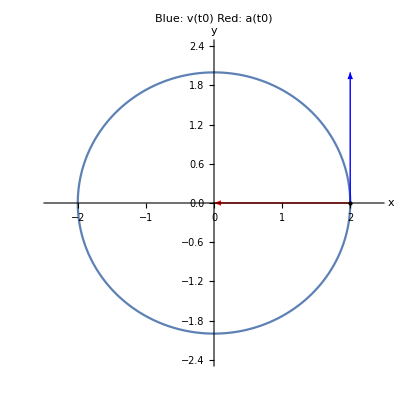

```mathematica
(*parameters for plotting*)R=2;ω=1;ϕ0=0;

(*position*)
r[t_]:=R {Cos[ω t+ϕ0],Sin[ω t+ϕ0]};

v=r';
a=r'';
t0=0;
p0=r[t0];
v0=v[t0];
a0=a[t0];

traj=ParametricPlot[Evaluate[r[τ]],{τ,0,2 Pi/ω},PlotRange->{{-1.2 R,1.2 R},{-1.2 R,1.2 R}},AxesLabel->{"x","y"},AspectRatio->1,PlotLabel->"Trajectory"];

Show[traj,Graphics[{Blue,Thick,Arrow[{p0,p0+v0/ω}],Red,Arrow[{p0,p0+a0/ω^2}],Black,PointSize[Large],Point[p0]}],PlotLabel->"Blue: v(t0)   Red: a(t0)"]
```